```mathematica
f =u/.NDSolve[{u''[x]+u'[x] - 2 u[x] == 0,u[0]==2,u[1]==Exp[1] + Exp[-2]},u, {x, 0, 1}][[1]]
```

InterpolatingFunction[…]

```mathematica
numS =
{{1,2.85362},{0.947368,2.7293},{0.894737,2.61379},{0.842105,2.50691},{0.789474,2.40851},{0.736842,2.3185},{0.684211,2.23682},{0.631579,2.16345},{0.578947,2.09842},{0.526316,2.04182},{0.473684,1.99378},{0.421053,1.95448},{0.368421,1.92419},{0.315789,1.9032},{0.263158,1.8919},{0.210526,1.89076},{0.157895,1.90032},{0.105263,1.92121},{0.0526316,1.95415},{0,2}};
```

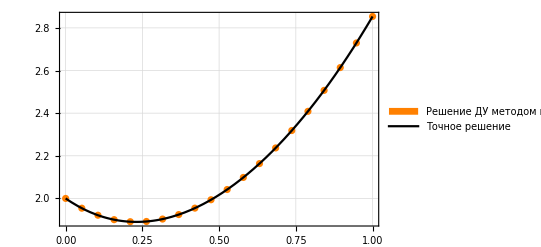

```mathematica
plNS = ListPlot[numS, PlotStyle->Orange, PlotLegends-> Grid[{{Graphics[{Orange,Disk[{0,0},1]},ImageSize->5],"Решение ДУ методом прогонки"}}],PlotTheme-> "Detailed"];

plES = Plot[f[x], {x, 0, 1}, Frame-> True, PlotStyle-> Black, PlotTheme-> "Detailed",PlotLegends->LineLegend[{Black}, {"Точное решение"}]];

plS = Show[ plNS, plES,PlotRange-> All]
```

```mathematica
Export["plS_20.pdf",plS];
Export["plS_20.jpg",plS];
```